# Mesh :: Infinite sheet of cells

## generating mesh with periodic boundary condition

```mathematica
(* subdividing XY grid *)
```

```mathematica
xL= 13.20/4;yL=15.20/4;cellNumX=6;
```

```mathematica
(* initial seed for a hexagon face *)
circlepts=0.45CirclePoints[{1,1},{1,0},6];
pts=Reverse[NestList[{0,0.45Sqrt[3]}+#&/@#&,circlepts,cellNumX-1],{3}];
```

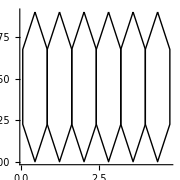

```mathematica
Graphics[{Black,Thick,Line[#~Append~First[#]]&/@pts},Axes->True,ImageSize->Small]
```

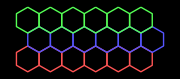

```mathematica
Block[{col2,col3},
col2=Map[0.45{Sqrt[3]/2,3/2}+#&,pts,{2}];
col3=Map[0.45{-Sqrt[3]/2,3/2}+#&,col2,{2}];
Show[{Graphics[{Thick,Lighter@Red,Line[#~Append~First[#]]&/@pts}],
Graphics[{Thick,Lighter@Blue,Line[#~Append~First[#]]&/@col2}],
Graphics[{Thick,Lighter@Green,Line[#~Append~First[#]]&/@col3}]},
Background->Black,ImageSize->Small]
]
```

### getting a hexagonal lattice

```mathematica
(* We generate a 2D hexagonal grid; Add a mirror Z plane; Make pairs and Construct Polyhedra *)
```

```mathematica
grid=Block[{temp,k=1,p=cellNumX},
NestList[(temp=Map[x↦0.45{If[OddQ[k],-1,1] (Sqrt[3]/2),3/2}+x,#,{2}];k++;
temp)&,pts,p-1]
];
```

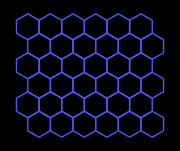

```mathematica
Graphics[{Thick,Lighter@Blue,Map[Line[#~Append~First[#]]&,grid,{2}]},Background->Black,ImageSize->Small]
```

```mathematica
xyzPts=Table[{Last[i],First[i],0.5},{i,Flatten[grid,2]}];
(*adding Z coordinate (height) to the polgonal face *)
```

```mathematica
Graphics3D[{Point@DeleteDuplicates@xyzPts},ImageSize->Small]
```

-Graphics3D-

```mathematica
nf=Nearest[DeleteDuplicates@xyzPts]
```

NearestFunction[…]

```mathematica
(nf[#,{All,1.0 10^-15}]&/@DeleteDuplicates[xyzPts])//Counts@*Map[Length] (* # of pts for which keys are > 1 need merging because of 
very tiny numerical errors. All this could have been avoided in the first place *)
```

<|3→15,2→94,1→44|>

```mathematica
replacements=Dispatch@Flatten@
Map[Function[x,#-> Mean[x]&/@x],
SortBy[Cases[Gather[DeleteDuplicates@xyzPts,EuclideanDistance[#1,#2]≤ 1.0 10^-15&],x_/;Length[x]>1],
First]
]
```

Dispatch[…]

```mathematica
(*replacements=Dispatch@Flatten[(x↦First[x]-> #&/@Rest[x])/@Cases[Gather[DeleteDuplicates@Flatten[grid,2],EuclideanDistance[#1,#2]≤ 1.0 10^-15&],
x_/;Length[x]>1],1]*)
```

```mathematica
xyzPts=xyzPts/.replacements;
```

```mathematica
Print[Length@DeleteDuplicates@xyzPts]
Graphics3D[Point@DeleteDuplicates@xyzPts,ImageSize->Small]
```

96

-Graphics3D-

```mathematica
nf=Nearest[DeleteDuplicates@xyzPts]
```

NearestFunction[…]

```mathematica
Apply[And]//@(Map[Through[{Apply[SameQ],Apply[Equal]}[#]]&]@Cases[
nf[#,{All,1.0 10^-15}]&/@DeleteDuplicates[xyzPts],
x_/;Length[x]>1])(*if value is true then the polygons have successfully shared common vertices *)
```

True

```mathematica
XYZgrid=ArrayReshape[xyzPts,Dimensions[grid]/.{x___,y_}:> {x,3}];
```

```mathematica
Graphics3D[{Opacity[0.2],Blue,Polygon/@XYZgrid},Axes->True,ImageSize->Small]
```

-Graphics3D-

```mathematica
(* Adding a mirror Z plane; putting vertical edges between the top and bottom faces and constructing individual polyhedrons or cells;Later we can add some noise to displace vertices from regularity *)
```

```mathematica
Grid[{{Graphics3D[{{XYZColor[0,0,1,0.25],Thick,Polygon/@XYZgrid},
{XYZColor[0,0,0,0.25],Thick,Polygon/@Map[#-{0,0,0.5}&,XYZgrid,{3}]}},
Axes-> True,ImageSize->Small],
Graphics3D[{{XYZColor[0,0,1,0.5],Thick,Map[Line[#~Append~First[#]]&,XYZgrid,{2}]},{XYZColor[0,0,0,0.5],Thick,Map[Line[#~Append~First[#]]&,#,{2}]&@Map[#-{0,0,0.5}&,XYZgrid,{3}]}},
Axes-> True,ImageSize->Small]}}]
```

-Graphics3D- | -Graphics3D-

```mathematica
vertexNum=Length@xyzPts
```

216

### generating the hexagonal prism lattice

```mathematica
Clear@triangulateFaces;
triangulateFaces::header= "triangulateFaces takes in a list of all the faces of a cell and returns a triangulation for each face";
triangulateFaces[faces_]:=Block[{edgelen,ls,mean},
(ls=Partition[#,2,1,1];
edgelen=EuclideanDistance@@@ls;
mean=Total[edgelen*(Midpoint/@ls)]/Total[edgelen];
mean =mean~SetPrecision~10;
Map[Append[#,mean]&,ls])&/@faces
];
```

```mathematica
Pts=MapIndexed[{#2[[1]],#1}&,Flatten[Riffle[Flatten[XYZgrid,1],Flatten[Map[#-{0,0,1}&,XYZgrid,{3}],1]],1]];(* all gird pts labeled *)
```

```mathematica
(*an seed polyhedron*)
seedPolyhedra=Pts[[#]][[All,2]]&/@{{1,2,3,4,5,6},{7,12,11,10,9,8},Sequence@@NestList[#+1&,{1,7,8,2},4],{6,12,7,1}};
```

```mathematica
Graphics3D[{Directive[Blue,Opacity[0.25*1/GoldenRatio]],Polyhedron[seedPolyhedra]},Boxed->False,ImageSize->Tiny]
```

-Graphics3D-

```mathematica
indToPtsAssoc=<|Rule@@@Pts|>;(* Association of gridptLabel -> gridpt *)
```

```mathematica
(*we create our polyhedra mesh *)
initFace={{1,2,3,4,5,6},{7,12,11,10,9,8},Sequence@@NestList[#+1&,{1,7,8,2},4],{6,12,7,1}};
faceListInd=NestList[#+12&,initFace,(cellNumX*cellNumX)-1];
faceListCoords=MapAt[Lookup[indToPtsAssoc,#]&,faceListInd,{All,All,All}];
firstPolyhedra=First@faceListCoords;
Graphics3D[{Directive[Blue,Opacity[0.25*1/GoldenRatio]],Polyhedron@Flatten[triangulateFaces[firstPolyhedra],1]},ImageSize->Tiny,Boxed->False]
```

-Graphics3D-

```mathematica
(*wireframe mesh rendering*)
Graphics3D[{Line@Flatten[(triangulateFaces/@faceListCoords),2]},ImageSize->Small]
```

-Graphics3D-

```mathematica
(*polyhedra mesh rendering*)
Graphics3D[{Directive[Blue,Opacity[0.2*1/GoldenRatio]],Polyhedron@Flatten[triangulateFaces/@faceListCoords,2]},ImageSize->Small]
```

-Graphics3D-

```mathematica
(col=ColorData["Rainbow"]/@Rescale[#,{Min[#],Max[#]},{0,1}]&[Flatten@XYZgrid[[All,All,1,2]]])//Partition[#,cellNumX]&//MatrixForm
```

(RGBColor[0.2836363636363637, 0.16658272727272722, 0.7120521818181818] | RGBColor[0.2805936363636363, 0.5226316363636361, 0.7796697272727274] | RGBColor[0.4526351818181815, 0.7095047272727272, 0.5131467272727277] | RGBColor[0.721312727272727, 0.738694090909091, 0.2921964545454547] | RGBColor[0.9011811818181817, 0.5711112727272732, 0.21431218181818193] | RGBColor[0.857359, 0.131106, 0.132128]
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.24468436363636364, 0.34889145454545445, 0.8118174545454545] | RGBColor[0.35055981818181803, 0.6429982727272725, 0.6627781818181822] | RGBColor[0.581950818181818, 0.7399549090909091, 0.38097727272727294] | RGBColor[0.8384345454545452, 0.6890935454545456, 0.24538763636363642] | RGBColor[0.8893551818181819, 0.36627890909090943, 0.1748141818181819]
RGBColor[0.2836363636363637, 0.16658272727272722, 0.7120521818181818] | RGBColor[0.2805936363636363, 0.5226316363636361, 0.7796697272727274] | RGBColor[0.4526351818181815, 0.7095047272727272, 0.5131467272727277] | RGBColor[0.721312727272727, 0.738694090909091, 0.2921964545454547] | RGBColor[0.9011811818181817, 0.5711112727272732, 0.21431218181818193] | RGBColor[0.857359, 0.131106, 0.132128]
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.24468436363636364, 0.34889145454545445, 0.8118174545454545] | RGBColor[0.35055981818181803, 0.6429982727272725, 0.6627781818181822] | RGBColor[0.581950818181818, 0.7399549090909091, 0.38097727272727294] | RGBColor[0.8384345454545452, 0.6890935454545456, 0.24538763636363642] | RGBColor[0.8893551818181819, 0.36627890909090943, 0.1748141818181819]
RGBColor[0.2836363636363637, 0.16658272727272722, 0.7120521818181818] | RGBColor[0.2805936363636363, 0.5226316363636361, 0.7796697272727274] | RGBColor[0.4526351818181815, 0.7095047272727272, 0.5131467272727277] | RGBColor[0.721312727272727, 0.738694090909091, 0.2921964545454547] | RGBColor[0.9011811818181817, 0.5711112727272732, 0.21431218181818193] | RGBColor[0.857359, 0.131106, 0.132128]
RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.24468436363636364, 0.34889145454545434, 0.8118174545454545] | RGBColor[0.350559818181818, 0.6429982727272724, 0.6627781818181823] | RGBColor[0.5819508181818178, 0.739954909090909, 0.3809772727272731] | RGBColor[0.8384345454545451, 0.6890935454545457, 0.24538763636363647] | RGBColor[0.889355181818182, 0.36627890909090977, 0.17481418181818195])

```mathematica
indToPtsAssoc=AssociationThread[Range[Length@#],#]&[DeleteDuplicatesBy[Pts[[All,2]],N]];(* <| ptlabel -> pt .. |> *)
ptsToIndAssoc=<|Reverse[Normal@indToPtsAssoc,2]|>;(* <| pt -> ptlabel .. |> *)
```

```mathematica
facePartitions=DeleteMissing[Map[Lookup[ptsToIndAssoc,#]&,triangulateFaces/@faceListCoords,{3}],4];(*polyhedra faces represented as edges via usage of consecutive vertices *)
```

```mathematica
vertexformingFaces=Map[Lookup[ptsToIndAssoc,#]&,faceListCoords,{2}];
(* polyhedra represented as sets of vertex labels *)
```

```mathematica
cellNum=cellNumX^2;
```

```mathematica
cellVertexGrouping=AssociationThread[Range[cellNum],vertexformingFaces];
(* <|cell_index -> {{vertex labels ..} ..}|> *)
```

```mathematica
vertexToCell=<|ParallelMap[#->Union@Position[facePartitions,#][[All,1]]&,Range[Max@Keys@indToPtsAssoc]]|>;(* <| vertex -> {cells the vertex is a member of} .. |> *)
```

```mathematica
edges=DeleteDuplicatesBy[Flatten[(x↦Partition[#,2,1,1]&/@x)/@faceListCoords,2],Sort];(*edges in the mesh *)
```

```mathematica
faceListCoords = Values@Map[indToPtsAssoc,cellVertexGrouping,{3}]; 
(*all polyhedra represented by vertex coordinates*)
```

```mathematica
Graphics3D[{Directive[Opacity[0.6]],Thread[{col,Polyhedron@Flatten[#,1]&/@(triangulateFaces/@faceListCoords)}]},ImageSize->Small,Axes-> True]
```

-Graphics3D-

```mathematica
(* The mesh above is not stitched about the boundaries; we have to stitch the boundaries together *)
```

```mathematica
Volume@*Polyhedron@Flatten[triangulateFaces@faceListCoords[[#]],1]&/@Range[36]//MinMax
```

{0.52611,0.52611}

### Stitching Boundaries

```mathematica
(* finding boundary cells *)
```

```mathematica
ptsp=#->Mean@Flatten[Map[Most@Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}],1]&/@Range[cellNum];
```

```mathematica
bcellsH=Transpose[Table[{k+1,cellNumX+k},{k,cellNumX,cellNumX*(cellNumX-2),cellNumX}]];
bcells=Union[Range[cellNumX]~Join~Range[cellNum-cellNumX +1,cellNum]~Join~Flatten[bcellsH]];
```

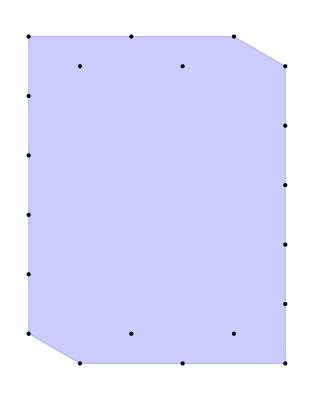

```mathematica
Show[{ConvexHullMesh[#,MeshCellStyle->{1->Blue,2->Directive[{Opacity[0.2],Blue}]}],Graphics[{Black,PointSize[Medium],Point[#]}]},ImageSize-> Tiny]&[Part[Values[ptsp],bcells]]
```

```mathematica
Length[bcells]
```

20

```mathematica
(* lets specify some limits for the boundaries *)
```

```mathematica
Union[Flatten@faceListCoords[[1]][[All,All,1]]][[1]](*left poly*)
```

0.

```mathematica
Union[Flatten@faceListCoords[[33]][[All,All,1]]][[3]](*right poly*)
```

4.05

```mathematica
Union[Flatten@faceListCoords[[7]][[All,All,2]]][[2]](*down poly*)
```

0.0602886

```mathematica
Union[Flatten@faceListCoords[[6]][[All,All,2]]][[4]](*up poly*)
```

4.73683

```mathematica
xLim={0.,4.05};
yLim={0.06028856829700263,4.736825748732972};
```

```mathematica
Graphics3D[{
{Blue,Opacity[0.1],Polyhedron@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}]&/@bcells[[1;;6]]},
{Black,Opacity[0.25],InfinitePlane[{{xLim[[1]],0,0},{xLim[[1]],1,0},{xLim[[1]],1,1}}]},
{Blue,Opacity[0.1],Polyhedron@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}]&/@bcells[[-6;;]]},
{Black,Opacity[0.25],InfinitePlane[{{xLim[[2]],0,0},{xLim[[2]],1,0},{xLim[[2]],1,1}}]},
{Blue,Opacity[0.1],Polyhedron@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}]&/@First@bcellsH},
{Black,Opacity[0.25],InfinitePlane[{{0,yLim[[1]],0},{1,yLim[[1]],0},{1,yLim[[1]],1}}]},
{Blue,Opacity[0.1],Polyhedron@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}]&/@Last@bcellsH},
{Black,Opacity[0.25],InfinitePlane[{{0,yLim[[2]],0},{1,yLim[[2]],0},{0,yLim[[2]],1}}]}
},ImageSize->Small,PlotRange->{{0,4.3},{-0.4,4.75},{-0.5,0.5}},Axes-> True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
(*We need a transformation matrix for each flagged cell -> this can be obtained by subtracting pt coordinates from the boundary limits;
storage matrix needs to be created for each flagged cell -> nearest neighbour function to be used for pts that pass boundary limits;*)
```

```mathematica
(*we choose two boundaries to create a nearest function to stitch the opposite boundaries *)
nearestFunc=Nearest@DeleteDuplicates@Flatten[DeleteDuplicates@Flatten[
Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}],1]&/@Join[Range@cellNumX,Last@bcellsH],1]
```

NearestFunction[…]

```mathematica
With[{xlim2= xLim[[2]],ylim1= yLim[[1]],ylim2= yLim[[2]]},
periodicRules=
Dispatch[{{x_/;x≥xlim2,y_/;y≤ylim1,z_}:> First@nearestFunc[{x-xlim2,y+(ylim2-ylim1),z}],
{x_/;x≥xlim2,y__}:>First@nearestFunc[ {x-xlim2,y}],
{x_,y_/;y≤ylim1,z_}:> First@nearestFunc[{x,y+(ylim2-ylim1),z}]}];

transformRules=Dispatch[{{x_/;x≥xlim2,y_/;y≤ylim1,_}:> {xlim2,-(ylim2-ylim1),0.},
{x_/;x≥xlim2,y__}:>{xlim2,0.,0.},
{x_,y_/;y≤ylim1,z_}:> {0.,-(ylim2-ylim1),0.},
{___Real}:> {0.,0.,0.}
}];
{periodicRules,transformRules}
]
```

{Dispatch[…],Dispatch[…]}

```mathematica
With[{xlim2= xLim[[2]],ylim1= yLim[[1]],ylim2= yLim[[2]]},
Graphics3D[
{Function[ind,{
{Red,PointSize[0.03],Point/@(Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[ind],{2}] /.periodicRules)}
}]/@Join[First@bcellsH,Range[cellNum-cellNumX +1,cellNum]],
{Blue,Opacity[0.1],Polyhedron@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}]&/@Join[Range@cellNumX,Range[cellNum-cellNumX +1,cellNum],
First@bcellsH,Last@bcellsH]},
{Green,Opacity[0.15],InfinitePlane[{{0,0,0},{0,1,0},{0,1,1}}],InfinitePlane[{{xlim2,0,0},{xlim2,1,0},{xlim2,1,1}}],
InfinitePlane[{{0,ylim1,0},{1,ylim1,0},{1,ylim1,1}}],InfinitePlane[{{0,ylim2,0},{1,ylim2,0},{0,ylim2,1}}]}},
ImageSize->Small,Axes-> True,PlotRange->{{-0.1,xlim2},{ylim1,ylim2},{-1.5,1.0}}
]
]
```

-Graphics3D-

```mathematica
exampleCell=1;
Block[{cvg=cellVertexGrouping[exampleCell],tMat},
Print["wrapping coordinates around using nearest neighbours"];
Print[Map[Lookup[indToPtsAssoc,#]&,cvg,{2}]/.periodicRules//Graphics3D[{XYZColor[0,0,1,0.5],PointSize[0.05],#},ImageSize->Tiny]&@*Map[Point]];
tMat=(Map[Lookup[indToPtsAssoc,#]&,cvg,{2}]/.transformRules);
Print["wrapped coordinates transformed to geometrically correct positions"];
Print@Graphics3D[{{PointSize[0.05],Opacity[0.25],Red,Point/@Map[Lookup[indToPtsAssoc,#]&,cvg,{2}]},
{PointSize[0.03],Blue,Point/@((Map[Lookup[indToPtsAssoc,#]&,cvg,{2}]/.periodicRules )+tMat)}},
ImageSize->Tiny];
]
```

wrapping coordinates around using nearest neighbours

-Graphics3D-

wrapped coordinates transformed to geometrically correct positions

-Graphics3D-

```mathematica
flaggedCells={1}~Join~First@bcellsH~Join~Range[cellNum-cellNumX +1,cellNum]
```

{1,7,13,19,25,31,32,33,34,35,36}

```mathematica
flaggedCellsTransPts = Function[ind,ind->(Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[ind],{2}] /.transformRules)]/@flaggedCells;
flaggedCellsStoragePts=Function[ind,ind->(Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[ind],{2}] /.periodicRules)]/@flaggedCells;
```

```mathematica
Graphics3D[{PointSize[0.025],XYZColor[0,0,1,0.7],
Map[Point,flaggedCellsStoragePts[[#,2]]&/@Range[Length@flaggedCells],{2}]},
ImageSize->Small]
```

-Graphics3D-

```mathematica
AssociateTo[cellVertexGrouping,MapAt[ptsToIndAssoc,flaggedCellsStoragePts,{All,2,All,All}]];
```

```mathematica
Block[{exampleCell=13,pos},
pos=First@@Position[flaggedCellsTransPts,exampleCell];
Graphics3D[{{Green,Opacity[0.5],PointSize[0.05],Point/@#},
{Black,Opacity[0.75],PointSize[0.025],Point/@(#+Values[flaggedCellsTransPts[[pos]]])}},
ImageSize->Small]&[Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[exampleCell],{2}]]
]
```

-Graphics3D-

```mathematica
faceListCoords =Map[indToPtsAssoc,cellVertexGrouping,{3}];
```

```mathematica
faceListCoords=Merge[{faceListCoords,<|flaggedCellsTransPts|>},Total];
faceListCoords=Values@faceListCoords;
```

```mathematica
Graphics3D[{Directive[Opacity[0.6]],Thread[{col,Polyhedron@Flatten[#,1]&/@(triangulateFaces/@faceListCoords)}]},
ImageSize->Small,Axes-> True]
```

-Graphics3D-

```mathematica
(* the mesh above is complete and is wrapped around the boundaries to form an infinite sheet of cells *)
```

```mathematica
edges=DeleteDuplicatesBy[Flatten[(x↦Partition[#,2,1,1]&/@x)/@faceListCoords,2],Sort];(* mesh edges *)
```

```mathematica
indToPtsAssoc=AssociationThread[Range[Length@#],#]&[DeleteDuplicates[Flatten[faceListCoords,2]]];(* <| vertex_labels -> vertex_pts |> *)
```

```mathematica
ptsToIndAssoc=<|Reverse[Normal@indToPtsAssoc,2]|>;
(* <| vertex_pts -> vertex_labels |>*)
```

```mathematica
cellVertexGrouping=AssociationThread[Range[Length@#],#]&[Map[Lookup[ptsToIndAssoc,#]&,faceListCoords,{2}]];
(* <|cell -> {{face vertex labels ..} ..}|>*)
```

```mathematica
vertexToCell=GroupBy[
Reverse[Flatten[Thread/@MapAt[Union@*Flatten,Normal[cellVertexGrouping],{All,2}]],2],
First-> Last];
```

```mathematica
(* <| vertex -> neighbouring cells .. |> *)
```

```mathematica
(* no duplicate pts found within tiny δ's *)
```

```mathematica
Volume@*Polyhedron@Flatten[triangulateFaces@faceListCoords[[#]],1]&/@Range[36]//MinMax
```

{0.52611,0.52611}

```mathematica
DeleteCases[
Lookup[ptsToIndAssoc,#]&/@
With[{vals=Values@indToPtsAssoc},
With[{nearest=Nearest[vals]},
nearest[#,{2,1.0 10^-15}]&/@vals
]
],x_/;Length[x]==1]//Length
```

0

```mathematica
Count[ Lookup[ptsToIndAssoc,#]&/@
With[{vals=DeleteDuplicates@Flatten[edges,1]},
With[{nf=Nearest@vals},
nf[#,{2,1.0 10^-15}]&/@vals
]
],{Repeated[_Integer,{2,∞}]}]
```

0

```mathematica
Length[
With[{vals=DeleteDuplicates@Flatten[edges,1]},
With[{nf=Nearest@vals},
nf[#,{2,1.0 10^-15}]&/@vals
]
]~DeleteCases~{{___Real}}
]
```

0

### check whether normals of triangulations are pointing outwards i.e. faces are oriented c.c.w

```mathematica
plts=Function[ind,
triangles=Triangle/@Flatten[triangulateFaces@faceListCoords[[ind]],1];trinormals=First@Region`Mesh`MeshCellNormals[DiscretizeGraphics@*Graphics3D@#,2]&/@triangles;tricents=RegionCentroid@*DiscretizeGraphics@*Graphics3D/@triangles;arrows=MapThread[Arrow[{#1,#1+0.5#2}]&,{tricents,trinormals}];Graphics3D[{{Opacity[0.1],Blue,triangles},Red,arrows},ImageSize->Small]]/@Range[cellNum];
```

```mathematica
ListAnimate[plts,SaveDefinitions->True]
```

### create the second layer of cells

```mathematica
shiftedpos=
Block[{keys,shift=1.4},
DeleteDuplicates@Flatten[
(keys=#;Thread[keys->(#-{0,0,shift}&/@Lookup[indToPtsAssoc,keys])])&/@Values@cellVertexGrouping⟦All,1⟧,
1]
];
```

```mathematica
nkeys=With[{mx=Max[Keys@indToPtsAssoc]},
Thread[#->Range[mx+1,mx+Length@#]]
]&[Keys@shiftedpos];
```

```mathematica
AssociateTo[indToPtsAssoc,Thread[Values@nkeys->Values@shiftedpos]];
```

```mathematica
newpolyinds=With[{mx=Length@cellVertexGrouping},
Thread[Range[mx+1,mx+Length@#]->#]&@({#2,#1,##3}&@@@Map[Reverse,Values[cellVertexGrouping/.Dispatch[nkeys]],{2}])
];
```

```mathematica
AssociateTo[cellVertexGrouping,newpolyinds];
```

```mathematica
bkeys={45,46,50,51,52,57,58};
```

```mathematica
typeb=Polyhedron/@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[[bkeys]]//Values,{2}]//Graphics3D[{EdgeForm[{Thickness[0.005],Black}],Opacity[0.2],Green,#},ImageSize->Small]&
```

-Graphics3D-

```mathematica
typec=Polyhedron/@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[[Range[cellNum+1,2cellNum]~Complement~bkeys]]//Values,{2}]//Graphics3D[{EdgeForm[{Thickness[0.005],Black}],Opacity[0.15],Blue,#},ImageSize->Small]&
```

-Graphics3D-

```mathematica
typea=Polyhedron/@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[[;;cellNum]]//Values,{2}]//Graphics3D[{EdgeForm[{Thickness[0.005],Black}],Opacity[0.06],Red,#},ImageSize->Small]&
```

-Graphics3D-

```mathematica
Show[typea,typeb,typec,Boxed->False,ImageSize->Medium]
```

-Graphics3D-

```mathematica
typea=Values[Polyhedron@Flatten[#,1]&@*triangulateFaces/@(Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[[;;cellNum]],{2}])]//Graphics3D[{EdgeForm[{Thin,Black}],Opacity[0.05],Red,#},ImageSize->Small]&
```

-Graphics3D-

```mathematica
typeb=Values[Polyhedron@Flatten[#,1]&@*triangulateFaces/@(Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[[bkeys]],{2}])]//Graphics3D[{EdgeForm[{Thin,Black}],Opacity[0.1],Green,#},ImageSize->Small]&
```

-Graphics3D-

```mathematica
typec=Values[Polyhedron@Flatten[#,1]&@*triangulateFaces/@(Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[[Range[cellNum+1,2cellNum]~Complement~bkeys]],{2}])]//Graphics3D[{EdgeForm[{Thin,Black}],Opacity[0.1],Blue,#},ImageSize->Small]&
```

-Graphics3D-

```mathematica
Show[typea,typeb,typec,ImageSize->Medium]
```

-Graphics3D-

```mathematica
AppendTo[faceListCoords,Map[Lookup[indToPtsAssoc,#]&,Values@cellVertexGrouping[[cellNum+1;;]],{2}]];
```

```mathematica
faceListCoords=FlattenAt[faceListCoords,cellNum+1];
```

```mathematica
edges=DeleteDuplicatesBy[Flatten[(x↦Partition[#,2,1,1]&/@x)/@faceListCoords,2],Sort];
```

```mathematica
ptsToIndAssoc=AssociationMap[Reverse,indToPtsAssoc];
```

```mathematica
vertexToCell=GroupBy[
Reverse[Flatten[Thread/@MapAt[Union@*Flatten,Normal[cellVertexGrouping],{All,2}]],2],
First-> Last];
```

```mathematica
plts=Function[ind,
triangles=Triangle/@Flatten[triangulateFaces@faceListCoords[[ind]],1];trinormals=First@Region`Mesh`MeshCellNormals[DiscretizeGraphics@*Graphics3D@#,2]&/@triangles;tricents=RegionCentroid@*DiscretizeGraphics@*Graphics3D/@triangles;arrows=MapThread[Arrow[{#1,#1+0.4#2}]&,{tricents,trinormals}];Graphics3D[{{Opacity[0.15],Blue,triangles},Thickness[0.007],Black,arrows},ImageSize->Small,Boxed->False]]/@Range[2cellNum];
```

```mathematica
ListAnimate[plts,SaveDefinitions->True]
```

```mathematica
(*DumpSave["D:\\LocalData\\hashmial\\VERTX\\multilayer\\create multilayer - smooth\\smoothgeometry.mx",{edges,indToPtsAssoc,ptsToIndAssoc,xLim,yLim,cellVertexGrouping,vertexToCell}];*)
```